# Análisis de Redes Sociales

Relaciones, relaciones y más relaciones...

Es un problema interdisciplinario: disciplinas sociales, matemáticas, estadística, computación, etc...
El tema de tener en cuenta las relaciones entre individuos empezó a finales de 1800 con Émile Durkheim (padre de la sociología) y Ferdinand Tönnies (también sociólogo).
Por 1930 Jacob Levy Moreno (psiquiatra Rumano) ---fudador del psicodrama--- desarrolla la sociometría a partir de la idea simple de representar personas como puntos y las relaciones entre ellas como líneas que unen los puntos.
Entre 1930 y 1960 hubo algunos trabajos de interes pero no fue hasta los años 60 que se empezó a trabajar el análisis de redes en forma por los científicos sociales.
Pero Leonhard Euler (matemático Suizo) ya había sentado los fundamentos de la teoría de grafos en 1736. Esta teoría es la representació matemática natural del sociograma de Moreno y es lo que le da un caracter formal y riguroso al análisis de redes (sociales o de otro tipo).
Hoy en dia el análisis de redes sociales es una mezcla de teoría de grafos con técnicas de representaciones visuales y de descripciones estadísticas de un conjunto de actores y sus relaciones. Todo esto gracias a la inmensa capacidad de cálculo y visualización de los computadores.
Lo interesante del análisis de redes (sociales) es que se puede aplicar al estudio de cualquier sistema (social) donde podamos definir relaciones entre sus componentes.
Las relaciones pueden ser físicas (cables) o no (amistad).

Software para análisis de redes?
	● Mathematica \[MathematicaIcon] (de la versión 7 en adelante, antes se utilizaba un paquete, Combinatorica, es obsoleto).
		Este es el que vamos a utilizar en clase (presentaciones y tutoriales).
		Los estudiantes del curso pueden utilizar otras herramientas.
	● UCINET, versión limitada grátis (https://sites.google.com/site/ucinetsoftware/home).
	● Gephi (http://wiki.gephi.org/index.php/Main_Page).
	● Pajek (http://pajek.imfm.si/doku.php).
	● R (varias librerías).
	● Python (varias librerías).
	● C (varias librerías).
	● En principio, cualquier paquete que haga estadística.

La siguiente gráfica es la representación visual de un grafo

```mathematica
dining=Import[FileNameJoin[{NotebookDirectory[],"Dining-table_partners.net"}]]
```

-Graphics-

La red es la descripción del grafo. Esta descripción utiliza un lenguaje que describe el contenido y la estructura.

Y todo esto sirve, en el fondo, para: detectar e interpretar patrones en los lazos entre actores.

# Definiciones

## Grafo

Un grafo está compuesto por un conjunto de nodos (actores vértices) y un conjunto de líneas (relaciones, bordes) entre pares de nodos.
El grafo representa la estructura de una red.

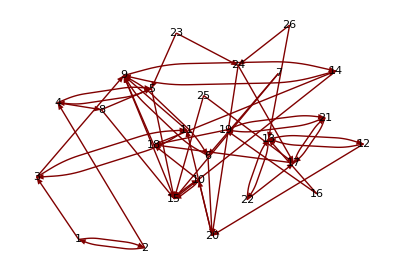

```mathematica
GraphPlot[dining,VertexLabeling->True]
```

El nodo es la estructura más pequeña del grafo, en general es representado por un número.
La línea representa una relación entre dos nodos
En el siguiente grafo:

```mathematica
Graph[{Style[1->2,Green],1->3,2->4,Style[2->1,Green]},EdgeStyle->Red]
```

-Graphics-

Tenemos nodos (puntos) y existe una relación entre algunos de ellos (línea verde o roja).

### Nodos

El nodo (actor, vértice), son las unidades discretas que se relacionan.
En general se consideran nodos del mismo tipo (redes de un solo modo ---one mode networks--- pero pueden haber redes de más de un modo (e.j: corporaciones y ONG, etc).

### Líneas

La línea (borde, arista) indican las relaciones entre nodos
En general se considera un solo tipo de relación entre nodos pero no es una restricción.

### Formalmente

Un grafo es un conjunto de nodos y sus bordes G={N,V}
Con 
	• N={1,2,...,n} el conjunto de nodos.
	• V={(i,j),...} el conjunto de relaciones (i,j) indica que hay una línea que va del nodo i al nodo j.
		Por cada tipo de relación posible, pueden haber máximo n (n-1) relaciones (elementos en V)
Una red es un grafo más la descripción de sus elementos, la red es el grafo más la información que lo acompaña.
La representación gráfica es una ayuda visual, muy útil, pero nada más.

#### Ejemplo

Este es un grafo de cinco nodos y 4 bordes

```mathematica
Graph[{1,2,3,4,5},{1->2,1->3,2->4,2->1}]
```

-Graphics-

Esta es la red de las compañeras de mesa

```mathematica
Grid[Join[{{HighlightGraph[dining,ImageSize->340],SpanFromLeft}},{{}},Transpose[{{"Niñas","Bordes (quisiera compartir mesa con)"},{VertexCount[dining],EdgeCount[dining]}}]],ItemSize->{{15,12},1},Alignment->Center]
```

-Graphics- | 
 | 
Niñas | 26
Bordes (quisiera compartir mesa con) | 52

La relación entre los nombres y el número de nodo

```mathematica
diningdata=StringReplace[ToString[FullForm[dining]],"Graph"->"List",1]//ToExpression;
TableForm[diningdata[[Sequence@@Flatten[{Position[diningdata,Rule[VertexLabels,___],∞],2}]]]//Sort]
```

1→Ada
2→Cora
3→Louise
4→Jean
5→Helen
6→Martha
7→Alice
8→Robin
9→Marion
10→Maxine
11→Lena
12→Hazel
13→Hilda
14→Frances
15→Eva
16→Ruth
17→Edna
18→Adele
19→Jane
20→Anna
21→Mary
22→Betty
23→Ella
24→Ellen
25→Laura
26→Irene

## Pareja (Dyad)

Un subconjunto de dos nodos unidos, o no,  por algún tipo de relación

```mathematica
GraphicsRow[{HighlightGraph[dining,{1,2},ImagePadding->20],HighlightGraph[dining,{12,24},ImagePadding->20]}]
```

-Graphics-

En un grafo (de un modo) las parejas posibles son:

```mathematica
GraphicsRow[{Subgraph[dining,{1,2}],Subgraph[dining,{2,4,9,3}],Subgraph[dining,{3,2}]},Frame->All]
```

-Graphics-

## Trio (Triad)

Un subconjunto de tres nodos unidos, o no,  por algún tipo de relación

```mathematica
GraphicsRow[{HighlightGraph[dining,{1,2,3},ImagePadding->20],HighlightGraph[dining,{12,23,24},ImagePadding->20],HighlightGraph[dining,{4,5,8},ImagePadding->20]}]
```

-Graphics-

En un grafo (de un modo) las triadas posibles (sin permutaciones) son:

```mathematica
GraphicsRow[{Subgraph[dining,{25,23,18}],Subgraph[dining,{12,23,24}],Subgraph[dining,{1,2,3}],Subgraph[dining,{4,5,8}]},Frame->All]
```

-Graphics-

## Grafo simple, no simple dirigido y no dirigido

Un grafo no dirigido (digrafo) es aquel donde toda relación es bidireccional, es simple si no presenta múltiples bordes y tampoco loops (relaciones yo con yo).

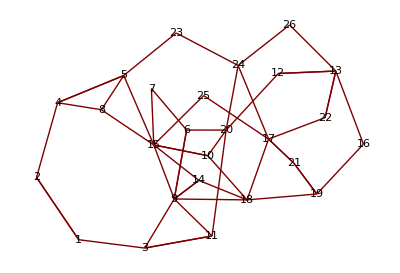

```mathematica
GraphPlot[dining,VertexLabeling->True,DirectedEdges->"False"]
```

Un grafo dirigido (grafo) es aquel donde toda relación es uni-direccional, puede tener loops (relaciones yo con yo).
Es simple si no presenta múltiples bordes ni loops.

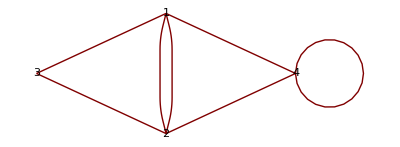

```mathematica
GraphPlot[{1->2,2->1,3->1,3->2,4->1,4->2,4->4},DirectedEdges->False,VertexLabeling->True]
```

# Notación

## Teoría de grafos

Cuando hablamos de nodos y líneas estamos utilizando teoría de grafos.
Suponemos que tenemos un conjunto de g nodos

N={n_1,n_2,…,n_g}

Con un conjunto de L relaciones entre ellos

L={l_1,l_2,…,l_L}
0≤ L ≤ g(g-1)

con l_i entendido como n_j→n_k.
El grafo se nota

G={N,L}

Si tenemos más de un tipo de relación, utilizamos varios L

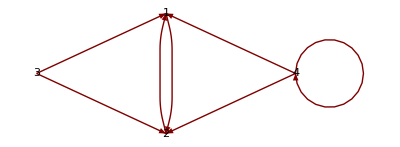

```mathematica
GraphPlot[{1->2,2->1,3->1,3->2,4->1,4->2,4->4},DirectedEdges->True,VertexLabeling->True]
```

N={1,2,3,4}

L={1→2,2→1,3→1,3→2,4→1,4→2,4→4}

### Grafos en Mathematica 9 \[MathematicaIcon]

Mathematica tiene bastantes herramientas para manejar grafos, la documentación la pueden encontrar en:
	Help → Documentation Center → Mathematics and Algorithms → Graphs & Networks
	ó escriban Graph y F1 en una celda de input (el estado por defecto)

Graph |

| Graph[{e_1,e_2,…}]
yields a graph with edges e_j.
 | Graph[{v_1,v_2,…},{{e_1,e_2,…}]
yields the graph with vertices v_i and edges e_j. 
 | Graph[{…,w_i[v_i,…],…},{…,w_j[e_j,…],…}]
yields a graph with vertex and edge properties defined by the symbolic wrappers w_k.

En Mathematica: 
	• los {} se utilizan para delimitar listas (son las estructuras de datos básicas).
	• los [] se utilizan para agrupar los argumentos de una función
entonces, Graph es una función, que recibe uno o dos argumentos (los argumentos son listas).

La primera opción nos sirve cuando queremos construir un grafo en el que todos los nodos tienen almenos una conección.
La notación es:
	• e_k=v_i->v_j para grafos dirigidos (-> se hace tecleando Esc de Esc)
	•  e_k=v_i<->v_j para grafos no dirigidos (<-> se hace tecleando Esc ue Esc)
En otras palabras, solo tenemos que darle la lista de relaciones.

#### Listas en Mathematica

Las listas son la estructura de datos básica de Mathematica. Son contenedores muy versátiles y fáciles de manejar.
Al ojo se identifican por los delimitadores {y }.
Se pueden escribir a mano (solo recomendable para listas pequeñas)

```mathematica
{3,2,4,3}
```

o se pueden construir con una regla, utilizando varias funciones propias de Mathematica (built-in functions)
	• Table
	• Array
	• Range
	• ...
Algo que tienen en común todas estas funciones es que requieren un iterador; así se le llama a la expresión que le indica a Mathematica que uno quiere cambiar una variable en una tarea repetitiva.
Hay 4 formas básicas para el iterador (los iteradores son listas y tienen sentido como argumento de una función).
	• {max} indica que queremos max copias

```mathematica
Table["jorge",{5}]
```

{jorge,jorge,jorge,jorge,jorge}

• {i,max} indica que queremos que i cambie de valor de 1 a max, cada cambio incrementa a i en 1 (i es un dummy)

```mathematica
Table[i/(i+1),{i,5}]
```

{1/2,2/3,3/4,4/5,5/6}

• {i,min,max} indica que queremos que i cambie de valor de min a max, cada cambio incrementa a i en 1 (i es un dummy)

```mathematica
Table[i+a,{i,-5,5}]
```

{-5+a,-4+a,-3+a,-2+a,-1+a,a,1+a,2+a,3+a,4+a,5+a}

• {i,min,max,di} indica que queremos que i cambie de valor de min a max, cada cambio incrementa a i en di (i es un dummy)

```mathematica
Table[i,{i,0,1,.1}]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

#### Ejemplo:

Construyamos un grafo línea, aquel donde el nodo i->i+1
Esta sería la lista de vértices

```mathematica
linea=Table[i->i+1,{i,25}]
```

{1->2,2->3,3->4,4->5,5->6,6->7,7->8,8->9,9->10,10->11,11->12,12->13,13->14,14->15,15->16,16->17,17->18,18->19,19->20,20->21,21->22,22->23,23->24,24->25,25->26}

```mathematica
Graph[linea]
```

-Graphics-

La segunda opción es para construir un grafo en el que no todos los nodos tienen almenos una conección

Ejemplo: construyamos un grafo estrella, aquel donde todos apuntan al nodo 1, junto con dos nodos que están conectado entre si y un nodo suelto
Esta sería la lista de vértices

```mathematica
star=Table[i+1<->1,{i,25}]
```

{2<->1,3<->1,4<->1,5<->1,6<->1,7<->1,8<->1,9<->1,10<->1,11<->1,12<->1,13<->1,14<->1,15<->1,16<->1,17<->1,18<->1,19<->1,20<->1,21<->1,22<->1,23<->1,24<->1,25<->1,26<->1}

```mathematica
star=Append[star,27<->1]
```

{2<->1,3<->1,4<->1,5<->1,6<->1,7<->1,8<->1,9<->1,10<->1,11<->1,12<->1,13<->1,14<->1,15<->1,16<->1,17<->1,18<->1,19<->1,20<->1,21<->1,22<->1,23<->1,24<->1,25<->1,26<->1,27<->1}

```mathematica
Graph[Range[27],star]
```

-Graphics-

### Dado un grafo en Mathematica 9 \[MathematicaIcon], ¿cómo extraemos el conjunto de nodos o el de relaciones?

Para preguntarle a Mathematica \[MathematicaIcon] cuál es la cantidad de nodos utilizamos la función VertexCount, para la lista de nodos VertexList

```mathematica
dining
```

-Graphics-

```mathematica
VertexCount[dining]
```

26

```mathematica
VertexList[dining]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26}

El número de bordes (conecciones), las obtenemos con EdgeCount, la lista de bordes con EdgeList

```mathematica
EdgeCount[dining]
```

52

```mathematica
EdgeList[dining]
```

{1->3,1->2,2->1,2->4,3->9,3->11,4->5,4->8,5->4,5->15,6->9,6->20,7->15,7->6,8->15,8->5,9->6,9->14,10->18,10->15,11->9,11->3,12->13,12->20,13->22,13->12,14->15,14->9,15->10,15->9,16->19,16->13,17->21,17->18,18->14,18->9,19->18,19->21,20->10,20->11,21->17,21->19,22->17,22->13,23->24,23->5,24->20,24->17,25->15,25->17,26->13,26->24}

## Sociométrica

Es una representación matricial, en principio la idea es tener x_ij como el valor de la reclación entre i y j.
Agrupamos estos valores en una matriz g×g

```mathematica
GraphPlot[{1->2,2->1,3->1,3->2,4->1,4->2,4->4},DirectedEdges->True,VertexLabeling->True]
```

-Graphics-

```mathematica
({{0, 1, 0, 0}, {1, 0, 0, 0}, {1, 1, 0, 0}, {1, 1, 0, 1}})
```

#### Matrices en Mathematica \[MathematicaIcon]

Mathematica no maneja matrices directamente, lo hace con la ayuda de listas (cosas separadas por comas que están encerradas entre {})
La forma de representar una matriz en matemática es con una lista de listas, cada lista interna (a nivel 2) representa una fila de la matriz.
Existen varias funciones para construir listas, las más utilizadas son Table o Array.
Existen muchísimas funciones para hacer operaciones sobre y con matrices (Help → Documentation Center → Mathematics and Algorithms → Matrices and Linear Algebra)

Ejemplo: escribamos la matriz (0 | 1 | 0 | 0
1 | 0 | 0 | 0
1 | 1 | 0 | 0
1 | 1 | 0 | 1)

```mathematica
mat={{0,1,0,0},
{1,0,0,0},
{1,1,0,0},
{1,1,0,1}} (*los cambios de línea no son necesarios*)
```

{{0,1,0,0},{1,0,0,0},{1,1,0,0},{1,1,0,1}}

Podemos preguntar por la 2da fila

```mathematica
mat[[2]]
```

{1,0,0,0}

Podemos preguntar por la 3ra columna

```mathematica
mat[[All,3]]
```

{0,0,0,0}

o por el elemento que está en la cuarta fila y en la primera columna

```mathematica
mat[[4,1]]
```

1

Ejemplo: escribamos la matriz que corresponde a

```mathematica
Graph[linea]
```

-Graphics-

Esta es la matriz de 25×25 (son 25 nodos) que tiene 0 en todo lado excepto en la diagonal que está por encima de la diagonal principal (la posición (i,i+1))
Una opción es construir una función que reciba dos números y devuelva 1 si y solo si el segundo argumento es el primero más 1

```mathematica
f[x_,y_]:=1/;y==x+1;
f[x_,y_]:=0;
```

```mathematica
matlinea=Table[f[i,j],{i,25},{j,25}]
```

{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

#### ¿Cómo pasamos de una matriz a un grafo (o vice versa) en Mathematica 9 \[MathematicaIcon]?

Hay dos funciones que nos ayudan en este problema:
	• AdjacencyGraph (para pasar de una matriz a un grafo)
	• AdjacencyMatrix (para obtener la matriz de adyacencia de un grafo)

```mathematica
AdjacencyMatrix[Graph[star]]
```

AdjacencyMatrix::graph: A graph object is expected at position 1 in AdjacencyMatrix[Graph[star]].

AdjacencyMatrix[Graph[star]]

```mathematica
%//Normal
```

{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
AdjacencyGraph[matlinea]
```

-Graphics-

## Algebráica

Es una notación muy útil cuando se tienen grafos con relaciones múltiples (de diferentes tipos).
Si en notación sociométrica tenemos que para la relación F

x_ijF=1

Utilizamos notación algebráica y escribimos

iFj

# Grafos y Matrices, resumen y aplicaciones

## Grafos

Un grafo es un modelo con relaciones no direccionadas.
Para definirlo necesitamos dos conjuntos :
El de los nodos

N={n_1,n_2,…,n_g}

Y un conjunto de L relaciones entr ellos

L={l_1,l_2,…,l_L}
0≤ L ≤ (g(g-1))/2
l_k=(n_i,n_j)

Esto también se conoce como la lista de adyacencia (las propiedades aplican para un grafo simple)

El grafo se nota

G={N,L}

## Matrices

Otra forma de representar la información en un grafo es via matrices.
Para un grafo simple o un digrafo, la matriz de adyacencia o sociomatriz, X, es una matriz cuadrada g×g, donde el elemento x_ij=0 si no hay relación entre el nodo n_i y n_j.
Si hay relación entre n_i y n_j, tenemos que x_ij=1.

```mathematica
small=ButterflyGraph[2];
```

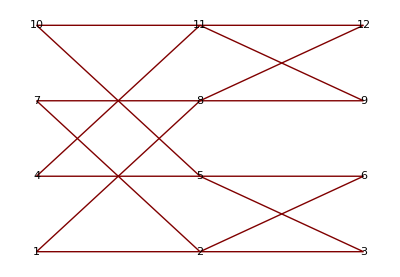

```mathematica
GraphPlot[small,VertexLabeling->True, Method->"SpringEmbedding"]
```

```mathematica
AdjacencyMatrix[small]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0)

La utilidad de utilizar representación matricial está en las propiedades de permutación y en las operaciones.

## Aplicaciones

### Subgrafos

Si tanto el conjunto de nodos y lineas  de un grafo G_s es subconjunto del grafo G decimos que G_s es subgrafo de G.
Hay tres formas de definir un subgrafo:
	◦ A partir de un subconjunto de nodos, en este caso los vínculos que se escojen son los que están entre esos nodos.
	◦ A partir de un subconjunto de vínculos
	◦ Algun criterio de la red.

#### ¿Cómo extraemos un subgrafo en Mathematica \[MathematicaIcon]?

Con Subgraph.

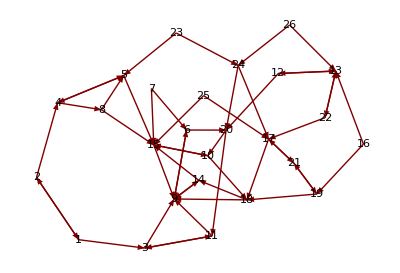

```mathematica
GraphPlot[dining,VertexLabeling->True]
```

```mathematica
Subgraph[dining,{1,2,3,4,9,15,8,20,23}]
```

-Graphics-

### Grado nodal

El grado de un nodo d(n_i), es el número de lineas incidentes a el (esta definición se puede expander a grafos dirigidos y con múltiples relaciones).
Equivalente, se puede pensar como el número de vecinos.

0≤ d(n_i)≤ g-1

El grado nos habla de la “actividad” del nodo, esto debe interpretarse dependiendo de la relación que estemos observando.
A veces tiene sentido hablar del grado medio

d^-=(∑_(i=1)^g d(n_i))/g=(2L)/g

y de la variancia, S_D^2, del grado

S_D^2=(∑_(i=1)^g (d(n_i)-d^-)^2)/(g-1)

Un grafo con variancia 0 se llama d-regular.

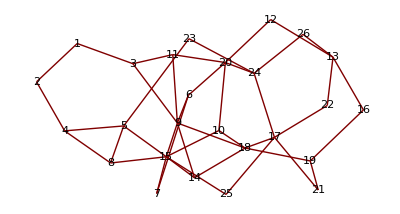

```mathematica
GraphPlot[diningund,VertexLabeling->True, Method->"SpringEmbedding"]
```

Para encontrar el grado uno puede contar las líneas que salen (out-degree) y llegan (in-degree) al grafo, esto no es práctico ni confiable con grafos grandes o densos.
En Mathematica \[MathematicaIcon] podemos utilizar la función VertexDegree (VertexInDegree, VertexOutDegree).

```mathematica
di=VertexDegree[diningund]
```

{2,2,3,3,4,3,2,3,6,3,3,2,4,3,7,2,5,5,3,5,2,2,2,4,2,2}

El grado medio

```mathematica
Mean[di]
```

42/13

```mathematica
Mean[di]//N
```

3.23077

La varianza del grado

```mathematica
Total[(di-%)^2]/(VertexCount[diningund]-1)
```

1.94462

```mathematica
Variance[di]
```

632/325

```mathematica
%//N
```

1.94462

La matriz de adyacencia nos permite encontrar el in-degree del nodo i sumando los elementos de la fila i; el out-degree lo encontramos sumando los elementos de la columan i. Si es un digrafo da lo mismo.

```mathematica
AdjacencyMatrix[diningund][[1]]
```

SparseArray[<2>,{26}]

```mathematica
Total[%]
```

2

```mathematica
Total/@AdjacencyMatrix[diningund]
```

{2,2,3,3,4,3,2,3,6,3,3,2,4,3,7,2,5,5,3,5,2,2,2,4,2,2}

### Densidad de un grafo

El número máximo de líneas en un grafo simple es

(g(g-1))/2

El número máximo de líneas en un grafo dirigido simple es

g(g-1)

La densidad, Δ, es la proporción de líneas que están en el grafo.
Para un grafo simple:

Δ=(2L)/(g(g-1))=d^-/(g-1)
0≤Δ≤ 1

Para un grafo dirigido simple:

Δ=L/(g(g-1))=d^-/(g-1)
0≤Δ≤ 1

Si la densidad es Δ=1 decimos que tenemos un grafo completo (todos con todos)
Para nuestro grafo...

```mathematica
(2EdgeCount[diningund])/(VertexCount[diningund](VertexCount[diningund]-1))//N
```

0.129231

```mathematica
%==Mean[di]/(VertexCount[diningund]-1)
```

True

### Walks, trails, paths (caminos, caminos y más caminos...)

#### Walks

Un walk es una secuencia que alterna entre nodos y lineas, comienza y termina en un nodo y cada nodo es incidente con la linea que lo precede y le sigue.

W = {n_i,l_j,n_k,…,n_m,l_n,n_p}
l_j={n_i,n_k},…, l_n={n_m,n_p}

```mathematica
HighlightGraph[diningund,{Labeled[1,"1"],Labeled[3,"3"],Labeled[9,"9"],Labeled[11,"11"],Labeled[14,"14"],Style[1<->3,Green],Style[3<->9,Green],Style[11<->9,Green],Style[14<->9,Red]}]
```

-Graphics-

W = {1,1<->3,3,3<->9,9,9<->14,14,14<->9,9,9<->11,11}

La longitud de un walk es el número de líneas que ocurren en el, para el ejemplo sería 5.
En grafos simples no hay ambiguedad posible para las líneas (no hay loops y las líneas no se repiten), es suficiente dar los nodos de manera ordenada para definir el walk.
Si existe un walk entre n_i y n_jdecimos que están conectados.

#### Trails, paths

Un trail es un walk en el que toda línea es distinta (se puede repetir nodo).
Si quisieramos ir de 1 a 11 pasando por 9...

```mathematica
HighlightGraph[diningund,{Labeled[1,"1"],Labeled[3,"3"],Labeled[9,"9"],Labeled[6,"6"],Labeled[20,"20"],Labeled[11,"11"],Style[1<->3,Green],Style[3<->9,Green],Style[6<->9,Green],Style[6<->20,Green],Style[20<->11,Green]}]
```

-Graphics-

En este caso W={1,3,9,6,20,11} y la longitud es 5.
Un path es un trail donde no se repiten nodos (en un path no se repite nada).

#### Caminos cerrados, tours y ciclos

Un camino cerrado es uno que termina en su mismo origen.
Un ciclo es un camino cerrado de longitud 3 o más que no repite líneas y solo repite el primer y último nodo.
El tour es un ciclo que utiliza cada línea del grafo al menos una vez.

```mathematica
HighlightGraph[diningund,Union[Table[Labeled[i,ToString[i]],{i,VertexCount[diningund]}],{Style[13<->12,Black],Style[13<->16,Black]},{Style[3<->1,Green],Style[4<->2,Green],Style[2<->1,Green],Style[4<->8,Green],Style[15<->8,Green],Style[15<->9,Green],Style[3<->9,Green]}]]
```

-Graphics-

Un camino cerrado: W={13,12,13,16,13}, de longitud 4
Un ciclo: W={3,1,2,4,8,15,9,3}, de longitud 7
Muchos tour, pero ninguno utiliza las línes solo una vez (Euleriano) o los nodos solo una vez (Hamiltoniano)

#### Caminos de longitud n

La potencia n de la matriz de adyacencia, X^n, nos da el número de caminos de lonjitud n entre los nodos i y j.
Para ver esto, recordemos que

x_ij^[2]=∑_(k=1)^g x_ik x_kj

El producto de la suma solo es diferente de 0 si  x_ik=x_kj=1, y esto quiere decir que i está conectado con k y k con j, entonces la suma de arriba cuenta la cantidad de caminos de longitud 2 entre i y j.

Para el siguiente grafo simple :

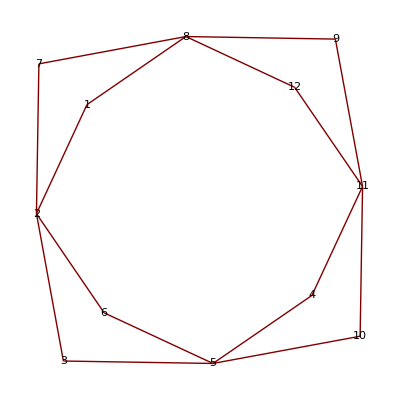

```mathematica
GraphPlot[small,VertexLabeling->True]
```

```mathematica
AdjacencyMatrix[small]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0)

```mathematica
m=AdjacencyMatrix[small];
```

Las potencias 2, 3, y 4 son :

```mathematica
Table[MatrixPower[m,i]//MatrixForm,{i,2,4}]
```

{(2 | 0 | 1 | 0 | 0 | 1 | 2 | 0 | 1 | 0 | 0 | 1
0 | 4 | 0 | 0 | 2 | 0 | 0 | 2 | 0 | 0 | 0 | 0
1 | 0 | 2 | 1 | 0 | 2 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 2 | 0 | 1 | 0 | 0 | 1 | 2 | 0 | 1
0 | 2 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 2 | 0
1 | 0 | 2 | 1 | 0 | 2 | 1 | 0 | 0 | 1 | 0 | 0
2 | 0 | 1 | 0 | 0 | 1 | 2 | 0 | 1 | 0 | 0 | 1
0 | 2 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 2 | 0
1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 2 | 1 | 0 | 2
0 | 0 | 1 | 2 | 0 | 1 | 0 | 0 | 1 | 2 | 0 | 1
0 | 0 | 0 | 0 | 2 | 0 | 0 | 2 | 0 | 0 | 4 | 0
1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 2 | 1 | 0 | 2),(0 | 6 | 0 | 0 | 2 | 0 | 0 | 6 | 0 | 0 | 2 | 0
6 | 0 | 6 | 2 | 0 | 6 | 6 | 0 | 2 | 2 | 0 | 2
0 | 6 | 0 | 0 | 6 | 0 | 0 | 2 | 0 | 0 | 2 | 0
0 | 2 | 0 | 0 | 6 | 0 | 0 | 2 | 0 | 0 | 6 | 0
2 | 0 | 6 | 6 | 0 | 6 | 2 | 0 | 2 | 6 | 0 | 2
0 | 6 | 0 | 0 | 6 | 0 | 0 | 2 | 0 | 0 | 2 | 0
0 | 6 | 0 | 0 | 2 | 0 | 0 | 6 | 0 | 0 | 2 | 0
6 | 0 | 2 | 2 | 0 | 2 | 6 | 0 | 6 | 2 | 0 | 6
0 | 2 | 0 | 0 | 2 | 0 | 0 | 6 | 0 | 0 | 6 | 0
0 | 2 | 0 | 0 | 6 | 0 | 0 | 2 | 0 | 0 | 6 | 0
2 | 0 | 2 | 6 | 0 | 2 | 2 | 0 | 6 | 6 | 0 | 6
0 | 2 | 0 | 0 | 2 | 0 | 0 | 6 | 0 | 0 | 6 | 0),(12 | 0 | 8 | 4 | 0 | 8 | 12 | 0 | 8 | 4 | 0 | 8
0 | 24 | 0 | 0 | 16 | 0 | 0 | 16 | 0 | 0 | 8 | 0
8 | 0 | 12 | 8 | 0 | 12 | 8 | 0 | 4 | 8 | 0 | 4
4 | 0 | 8 | 12 | 0 | 8 | 4 | 0 | 8 | 12 | 0 | 8
0 | 16 | 0 | 0 | 24 | 0 | 0 | 8 | 0 | 0 | 16 | 0
8 | 0 | 12 | 8 | 0 | 12 | 8 | 0 | 4 | 8 | 0 | 4
12 | 0 | 8 | 4 | 0 | 8 | 12 | 0 | 8 | 4 | 0 | 8
0 | 16 | 0 | 0 | 8 | 0 | 0 | 24 | 0 | 0 | 16 | 0
8 | 0 | 4 | 8 | 0 | 4 | 8 | 0 | 12 | 8 | 0 | 12
4 | 0 | 8 | 12 | 0 | 8 | 4 | 0 | 8 | 12 | 0 | 8
0 | 8 | 0 | 0 | 16 | 0 | 0 | 16 | 0 | 0 | 24 | 0
8 | 0 | 4 | 8 | 0 | 4 | 8 | 0 | 12 | 8 | 0 | 12)}

Hay 6 caminos de longitud 3 entre el nodo 2 y e l 3

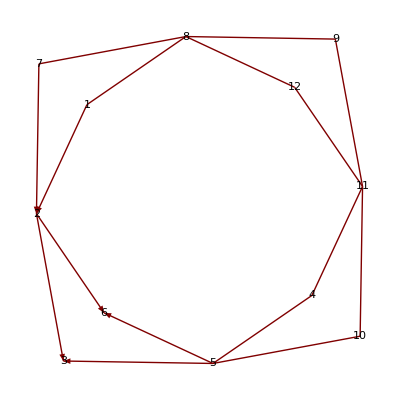

```mathematica
GraphPlot[{{1->2, "{2,1,2,3}"},1->8,{2->3, "{2,3,2,3}"},{2->6, "{2,6,2,3}"},4->5,4->11,{5->3, "{2,3,5,3}"},{5->6, "{2,6,5,3}"},{7->2,"{2,7,2,3}"},7->8,8->9,8->12,10->5,10->11,11->9,11->12},VertexLabeling->True]
```

### Grafos conectados y componentes

Un grafo está conectado si existe un camino entre cualquier par de nodos
Los subgrafos conectados de un grafo se llaman sus componentes.

```mathematica
disco=Graph[{1<->5,1<->6,6<->5,2<->4,3<->4}]
```

-Graphics-

Hay varias formas de saber si una red está conectada.
Una es gráficamente.
Otra es mirando la matriz de adyacencia y buscando “bloques”.

```mathematica
md=AdjacencyMatrix[disco];
md//MatrixForm
```

(0 | 1 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0)

Otra es construir X^[Σ]

X^[Σ]=∑_(i=1)^(g-1) X^[i]

```mathematica
MatrixForm[Table[MatrixPower[md,i],{i,Length[md]-1}]//Total]
```

(20 | 21 | 21 | 0 | 0 | 0
21 | 20 | 21 | 0 | 0 | 0
21 | 21 | 20 | 0 | 0 | 0
0 | 0 | 0 | 3 | 7 | 3
0 | 0 | 0 | 7 | 6 | 7
0 | 0 | 0 | 3 | 7 | 3)

Si alguno de los elementos de X^[Σ] es 0, quiere decir que no hay ningún camino de longitud g-1 entre esos dos nodos.

Uno le puede preguntar a Mathematica \[MathematicaIcon] cuáles son los componentes de un grafo

```mathematica
ConnectedComponents[disco]
```

{{5,1,6},{4,2,3}}

```mathematica
disco
```

-Graphics-

El número de componentes es la cantidad de elementos que tiene la partición

```mathematica
Length[ConnectedComponents[disco]]
```

2

Otra es haciendo análisis espectral (último módulo).

### Geodésicas y diámetro.

La geodésica, d(i,j), es la distancia más corta (en términos de caminos) entre dos nodos.
La exentricidad de un nodo es la geodésica más larga entre el y los demás nodos de la red.
El diámetro de un grafo es la geodésica más grande de todas.

```mathematica
GraphPlot[diningund,VertexLabeling->True, Method->"SpringEmbedding"]
```

-Graphics-

Estas son las geodésicas entre todos los nodos :

```mathematica
distancias=GraphDistanceMatrix[diningund];
```

```mathematica
MatrixForm[distancias]
```

(0 | 1 | 1 | 2 | 3 | 3 | 4 | 3 | 2 | 4 | 2 | 4 | 5 | 3 | 3 | 5 | 4 | 3 | 4 | 3 | 5 | 5 | 4 | 4 | 4 | 5
1 | 0 | 2 | 1 | 2 | 4 | 4 | 2 | 3 | 4 | 3 | 5 | 6 | 4 | 3 | 6 | 5 | 4 | 5 | 4 | 6 | 6 | 3 | 4 | 4 | 5
1 | 2 | 0 | 3 | 3 | 2 | 3 | 3 | 1 | 3 | 1 | 3 | 4 | 2 | 2 | 4 | 3 | 2 | 3 | 2 | 4 | 4 | 4 | 3 | 3 | 4
2 | 1 | 3 | 0 | 1 | 4 | 3 | 1 | 3 | 3 | 4 | 5 | 5 | 3 | 2 | 6 | 4 | 4 | 5 | 4 | 5 | 5 | 2 | 3 | 3 | 4
3 | 2 | 3 | 1 | 0 | 3 | 2 | 1 | 2 | 2 | 3 | 4 | 4 | 2 | 1 | 5 | 3 | 3 | 4 | 3 | 4 | 4 | 1 | 2 | 2 | 3
3 | 4 | 2 | 4 | 3 | 0 | 1 | 3 | 1 | 2 | 2 | 2 | 3 | 2 | 2 | 4 | 3 | 2 | 3 | 1 | 4 | 4 | 3 | 2 | 3 | 3
4 | 4 | 3 | 3 | 2 | 1 | 0 | 2 | 2 | 2 | 3 | 3 | 4 | 2 | 1 | 5 | 3 | 3 | 4 | 2 | 4 | 4 | 3 | 3 | 2 | 4
3 | 2 | 3 | 1 | 1 | 3 | 2 | 0 | 2 | 2 | 3 | 4 | 5 | 2 | 1 | 5 | 3 | 3 | 4 | 3 | 4 | 4 | 2 | 3 | 2 | 4
2 | 3 | 1 | 3 | 2 | 1 | 2 | 2 | 0 | 2 | 1 | 3 | 4 | 1 | 1 | 3 | 2 | 1 | 2 | 2 | 3 | 3 | 3 | 3 | 2 | 4
4 | 4 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 0 | 2 | 2 | 3 | 2 | 1 | 3 | 2 | 1 | 2 | 1 | 3 | 3 | 3 | 2 | 2 | 3
2 | 3 | 1 | 4 | 3 | 2 | 3 | 3 | 1 | 2 | 0 | 2 | 3 | 2 | 2 | 4 | 3 | 2 | 3 | 1 | 4 | 4 | 3 | 2 | 3 | 3
4 | 5 | 3 | 5 | 4 | 2 | 3 | 4 | 3 | 2 | 2 | 0 | 1 | 4 | 3 | 2 | 3 | 3 | 3 | 1 | 4 | 2 | 3 | 2 | 4 | 2
5 | 6 | 4 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 3 | 1 | 0 | 4 | 4 | 1 | 2 | 3 | 2 | 2 | 3 | 1 | 3 | 2 | 3 | 1
3 | 4 | 2 | 3 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 4 | 4 | 0 | 1 | 3 | 2 | 1 | 2 | 3 | 3 | 3 | 3 | 3 | 2 | 4
3 | 3 | 2 | 2 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 3 | 4 | 1 | 0 | 4 | 2 | 2 | 3 | 2 | 3 | 3 | 2 | 3 | 1 | 4
5 | 6 | 4 | 6 | 5 | 4 | 5 | 5 | 3 | 3 | 4 | 2 | 1 | 3 | 4 | 0 | 3 | 2 | 1 | 3 | 2 | 2 | 4 | 3 | 4 | 2
4 | 5 | 3 | 4 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 3 | 0 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 1 | 2
3 | 4 | 2 | 4 | 3 | 2 | 3 | 3 | 1 | 1 | 2 | 3 | 3 | 1 | 2 | 2 | 1 | 0 | 1 | 2 | 2 | 2 | 3 | 2 | 2 | 3
4 | 5 | 3 | 5 | 4 | 3 | 4 | 4 | 2 | 2 | 3 | 3 | 2 | 2 | 3 | 1 | 2 | 1 | 0 | 3 | 1 | 3 | 4 | 3 | 3 | 3
3 | 4 | 2 | 4 | 3 | 1 | 2 | 3 | 2 | 1 | 1 | 1 | 2 | 3 | 2 | 3 | 2 | 2 | 3 | 0 | 3 | 3 | 2 | 1 | 3 | 2
5 | 6 | 4 | 5 | 4 | 4 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 3 | 3 | 2 | 1 | 2 | 1 | 3 | 0 | 2 | 3 | 2 | 2 | 3
5 | 6 | 4 | 5 | 4 | 4 | 4 | 4 | 3 | 3 | 4 | 2 | 1 | 3 | 3 | 2 | 1 | 2 | 3 | 3 | 2 | 0 | 3 | 2 | 2 | 2
4 | 3 | 4 | 2 | 1 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 4 | 2 | 3 | 4 | 2 | 3 | 3 | 0 | 1 | 3 | 2
4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 1 | 2 | 3 | 1 | 2 | 2 | 1 | 0 | 2 | 1
4 | 4 | 3 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 3 | 4 | 3 | 2 | 1 | 4 | 1 | 2 | 3 | 3 | 2 | 2 | 3 | 2 | 0 | 3
5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 4 | 3 | 3 | 2 | 1 | 4 | 4 | 2 | 2 | 3 | 3 | 2 | 3 | 2 | 2 | 1 | 3 | 0)

La exentricidad de cada nodo :

```mathematica
Max/@distancias
```

{5,6,4,6,5,4,5,5,4,4,4,5,6,4,4,6,5,4,5,4,6,6,4,4,4,5}

El diamétro del grafo :

```mathematica
Max[%]
```

6

Para encontrar d(i,j) toca inspeccionar las potencias de la sociomatriz: d(i,j)=min_p x_ij^[p]>0
El diámetro es: max d(i,j)
Por qué las potencias?
Miremos qué ocurre cuando multiplicamos una matriz

Recordemos que 
	x[i,j]=0 si i y j no son vecinos (no hay caminino de longitud 1 entre ellos)
	x[i,j]=1 si i y j son vecinos (hay caminino de longitud 1 entre ellos)
La matriz de adyacencia nos dice cuántos cominos de longitud 1 hay y en donde están.
Miremos X^2

Miremos la diagonal
	(X^2)_(i,i)=∑_(j=1)^n x[i,j] x[j,i]
	Esto sólamente es diferente de 0 si x[i,j] =x[j,i]=1, entonces (X^2)_(i,i)=número de vecinos de i que pueden volver inmediatamente

Si la red es no dirigida es el número de vecinos

```mathematica
disco=Graph[Range[6],{Style[1<->5,Green],1<->6,6<->5,2<->4,Style[3<->4,Green]},VertexLabels->"Name" ,ImagePadding->12];
Row[{disco,(AdjacencyMatrix[disco].AdjacencyMatrix[disco])//MatrixForm}]
```

-Graphics-(2 | 0 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0
1 | 0 | 0 | 0 | 2 | 1
1 | 0 | 0 | 0 | 1 | 2)

Si la red es dirigida es el número de vecinos que tienen lazo recíproco

```mathematica
discodi=Graph[Range[6],{Style[1->5,Green],Style[5->1,Green],1->6,6->5,2->4,Style[3->4,Red]},VertexLabels->"Name" ,ImagePadding->12];
Row[{discodi,(AdjacencyMatrix[discodi].AdjacencyMatrix[discodi])//MatrixForm}]
```

-Graphics-(1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0)

Miremos fuera de la diagonal
	(X^2)_(i,j)=fila_i . columna_j=∑_(k=1)^n x[i,k] x[k,j]
	Esto sólamente es diferente de 0 si x[i,k] =x[k,j]=1, entonces (X^2)_(i,j)=número de nodos j tales que existe un nodo k que los conecta con i, es decir cuenta el número de intermediarios entre i y j

```mathematica
disco=Graph[Range[6],{Style[1<->5,Green],Style[1<->6,Green],6<->5,Style[2<->4,Green],Style[3<->4,Green]},VertexLabels->"Name" ,ImagePadding->12];
Row[{disco,(AdjacencyMatrix[disco].AdjacencyMatrix[disco])//MatrixForm}]
```

-Graphics-(2 | 0 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0
1 | 0 | 0 | 0 | 2 | 1
1 | 0 | 0 | 0 | 1 | 2)

```mathematica
discodi=Graph[Range[6],{Style[1->5,Green],Style[5->1,Green],1->6,6->5,2->4,3->4},VertexLabels->"Name" ,ImagePadding->12];
Row[{discodi,(AdjacencyMatrix[discodi].AdjacencyMatrix[discodi])//MatrixForm}]
```

-Graphics-(1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0)

Esto se puede generalizar, la potencia n de la matriz de adyacencia nos da el número de caminos de longitud n que hay entre dos nodos.